```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot,ListPlot}, ImageSize->Medium,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Interpolation *)
```

```mathematica
(* Problem (0) Animate a transformed torus given by a=2.5;  {(3+Cos[a*v])Sin[u],(3+Cos[v]) Cos[u], z=Sin[v]} along the trajectory interpolated from 
data0:={{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}} Use the texture below  *)
```

```mathematica
Text0:=-Graphics-
```

```mathematica
a=2.5;
```

```mathematica
s0[u_,v_]:={(3+Cos[a*v]) Sin[u],(3+Cos[v]) Cos[ u],Sin[ v]}
```

```mathematica
G0=ParametricPlot3D[s0[u,v],{u,0,2Pi},{v,0,2Pi},PlotStyle->Texture[Text0],Mesh->False]
```

-Graphics3D-

```mathematica
(* The origin *)
```

```mathematica
Zero=Graphics3D[{Red,PointSize[0.08],Point[{{0,0,0}}]}];
```

```mathematica
Show[G0,Zero]
```

-Graphics3D-

```mathematica
(* Along the  interpolating trajectory obtained from  *)
```

```mathematica
data0:={{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}}
```

```mathematica
xd0=Transpose[data0][[1]];
```

```mathematica
yd0=Transpose[data0][[2]];
```

```mathematica
zd0=Transpose[data0][[3]];
```

```mathematica
sd0x=Interpolation[xd0,Method->"Spline"];
```

```mathematica
sd0y=Interpolation[yd0,Method->"Spline"];
```

```mathematica
sd0z=Interpolation[zd0,Method->"Spline"];
```

```mathematica
(* 3D parametric function - trajectory *)
```

```mathematica
Traj0[t_]:={sd0x[t],sd0y[t],sd0z[t]} (* immediate evaluation *)
```

```mathematica
L0=Length[xd0];
```

```mathematica
plot0t=ParametricPlot3D[Traj0[t],{t,1,L0},PlotStyle->Purple ];
```

```mathematica
plot0tpoints=ListPointPlot3D[data0,PlotStyle->{PointSize[0.01],Blue}];
```

```mathematica
GTraj0=Show[{plot0t,plot0tpoints}]
```

-Graphics3D-

```mathematica
SurfacePosition0[u_,v_,s_]:=s0[u,v]+Traj0[s]
```

```mathematica
plots0[s_]:=ParametricPlot3D[SurfacePosition0[u,v,s],{u,0,2Pi},{v,0,2Pi},PlotRange->{{-10,10},{-10,10},{-10,10}},PlotStyle->Texture[Text0]]
```

```mathematica
Show[plots0[6],GTraj0]
```

-Graphics3D-

```mathematica
plotShow0[s_]:=Show[plots0[s],GTraj0]
```

```mathematica
Manipulate[plotShow0[s],{s,1,L0,0.1}]
```

```mathematica
(* Include *)
```

```mathematica
Text01:=-Graphics-; Text11:=-Graphics-; Text12:= -Graphics-;
```

```mathematica
Text1List={Text01,Text11,Text12}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotsT[s_,Tex_]:= ParametricPlot3D[SurfacePosition0[u,v,s],{u,0,2Pi},{v,0,2Pi},PlotRange->{{-10,10},{-10,10},{-10,10}},PlotStyle->Texture[Tex]]
```

```mathematica
plotShowsT[s_,Tex_]:=Show[plotsT[s,Tex],GTraj0]
```

```mathematica
Manipulate[plotShowsT[s,Tex],{s,1,L0,0.1},{Tex,Text1List}]
```

```mathematica
(* Problem (1) Interpolate a 3D data given by the heights of the explicit function z=f(x,y) using the synthetic data
data1=Table[Round[Exp[x2-y^2],0.01]{x,-1,1,0.25},{y,-1,2,0.25}]
Move the resulting surface along an interpolated curve 
through points pp1={0,0,0} and pp2={1,1,1} pp3={0.5,0.5,0.5}; pp4={0,3,2} 
 ListInterpolation[data,{{xmin,xmax,{ymin,ymax}}]
*)
```

```mathematica
pp1={0,0,0} ; pp2={1,0,0.5};pp3={0.7,0.8,0.9};pp4={0,3,2};
```

```mathematica
fsyn[x_,y_]:=x y Exp[x^2- y^2]
```

```mathematica
xmin1=-1;xmax1=1;ymin1=-1;ymax1=1;
```

```mathematica
stepx1=0.25;stepy1=stepx1;
```

```mathematica
data1=Table[Round[fsyn[x,y],0.01],{x,xmin1,xmax1,stepx1},{y,ymin1,ymax1,stepy1}];
```

```mathematica
MatrixForm[data1]
```

(1. | 1.16 | 1.06 | 0.64 | 0. | -0.64 | -1.06 | -1.16 | -1.
0.48 | 0.56 | 0.51 | 0.31 | 0. | -0.31 | -0.51 | -0.56 | -0.48
0.24 | 0.27 | 0.25 | 0.15 | 0. | -0.15 | -0.25 | -0.27 | -0.24
0.1 | 0.11 | 0.1 | 0.06 | 0. | -0.06 | -0.1 | -0.11 | -0.1
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.1 | -0.11 | -0.1 | -0.06 | 0. | 0.06 | 0.1 | 0.11 | 0.1
-0.24 | -0.27 | -0.25 | -0.15 | 0. | 0.15 | 0.25 | 0.27 | 0.24
-0.48 | -0.56 | -0.51 | -0.31 | 0. | 0.31 | 0.51 | 0.56 | 0.48
-1. | -1.16 | -1.06 | -0.64 | 0. | 0.64 | 1.06 | 1.16 | 1.)

```mathematica
(* x-y-range *)
```

```mathematica
DR1={{xmin1,xmax1},{ymin1,ymax1}};
```

```mathematica
GD1=ListPointPlot3D[data1,PlotStyle->{Orange,PointSize[0.05]},DataRange->DR1]
```

-Graphics3D-

```mathematica
(* Transpose the matrix to comply with ListInterpolation. *)
```

```mathematica
Tdata1=Transpose[data1];
```

```mathematica
f1=ListInterpolation[Tdata1,DR1]
```

InterpolatingFunction[…]

```mathematica
Zero=Graphics3D[{Red,PointSize[0.08],Point[{{0,0,0}}]}];
```

```mathematica
(* Plot the surface *)
```

```mathematica
TextEl=-Graphics-;
```

```mathematica
Ginter=Plot3D[f1[x,y],{x,xmin1,xmax1},{y,ymin1,ymax1},PlotStyle->{Blue,Opacity[0.7],Texture[TextEl]}]
```

-Graphics3D-

```mathematica
(* Superimpose  *)
```

```mathematica
GAll=Show[{GD1,Ginter,Zero},Boxed->True]
```

-Graphics3D-

```mathematica
(* Understand the structure of the modules below  *)
```

```mathematica
Listp=2{pp1,pp2,pp3,pp4}
```

{{0,0,0},{2,0,1.},{1.4,1.6,1.8},{0,6,4}}

```mathematica
(* Extract x,y,z from the data  *)
```

```mathematica
Extractxyz[data_]:=Module[{dataT,px,py,pz},
dataT=Transpose[data];
px=dataT[[1]];
py=dataT[[2]];
pz=dataT[[3]];
{px,py,pz}(*output=x,y,z*)]
```

```mathematica
{px,py,pz}=Extractxyz[Listp]
```

{{0,2,1.4,0},{0,0,1.6,6},{0,1.,1.8,4}}

```mathematica
(* Generate fx,fy,fz to compose a parametric function Traj1[s]  *)
```

```mathematica
Interpxyz[data_]:=Module[{px,py,pz,fx,fy,fz},
{px,py,pz}=Extractxyz[data]; 
fx=Interpolation[px];fy=Interpolation[py];fz=Interpolation[pz];{fx,fy,fz}(*output=3 interpolating functions*)]
```

```mathematica
{tx,ty,tz}=Interpxyz[Listp]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Traj1[s_]:={tx[s],ty[s],tz[s]}
```

```mathematica
GL1=ParametricPlot3D[Traj1[t],{t,1,4}]
```

-Graphics3D-

```mathematica
(* The line and the surface  *)
```

```mathematica
SG11=Show[GL1,Ginter]
```

-Graphics3D-

```mathematica
(* Convert the surface into the parametric form  *)
```

```mathematica
S1[u_,v_]:={u,v,f1[u,v]}
```

```mathematica
(* Check  *)
```

```mathematica
GP1=ParametricPlot3D[S1[x,y],{x,xmin1,xmax1},{y,ymin1,ymax1},PlotRange->1,BoxRatios->1]
```

-Graphics3D-

```mathematica
SurfacePosition1[u_,v_,t_]:=S1[u,v]+Traj1[t]
```

```mathematica
(* Check  *)
```

```mathematica
SurfacePosition1[1,1,1]
```

{1.,1.,1.}

```mathematica
Text1:=-Graphics-
```

```mathematica
Gfunction1[t_]:=ParametricPlot3D[SurfacePosition1[x,y,t],{x,xmin1,xmax1},{y,ymin1,ymax1},PlotStyle->Texture[Text1],Mesh->False]
```

```mathematica
(* Check  *)
```

```mathematica
Gfunction1[2.5]
```

-Graphics3D-

```mathematica
GShowAll[s_]:=Show[{GL1,Zero,Gfunction1[s]},PlotRange->{{-2,3},{-1,10},{0,5}}]
```

```mathematica
Manipulate[GShowAll[t],{t,1,4}]
```

```mathematica
(* Problem 2 *)
```

```mathematica
data0=Table[{Sin[3*t],Cos[4*t],t},{t,0,5,0.25}]
```

{{0.,1.,0.},{0.681639,0.540302,0.25},{0.997495,-0.416147,0.5},{0.778073,-0.989992,0.75},{0.14112,-0.653644,1.},{-0.571561,0.283662,1.25},{-0.97753,0.96017,1.5},{-0.858934,0.753902,1.75},{-0.279415,-0.1455,2.},{0.450044,-0.91113,2.25},{0.938,-0.839072,2.5},{0.922604,0.0044257,2.75},{0.412118,0.843854,3.},{-0.319519,0.907447,3.25},{-0.879696,0.136737,3.5},{-0.967808,-0.759688,3.75},{-0.536573,-0.957659,4.},{0.182599,-0.275163,4.25},{0.803784,0.660317,4.5},{0.993641,0.988705,4.75},{0.650288,0.408082,5.}}

```mathematica
GD2=ListPointPlot3D[data02, PlotStyle->PointSize[0.04]]
```

-Graphics3D-

```mathematica
ExtData0 = Extractxyz[data0]
```

{{0.,0.681639,0.997495,0.778073,0.14112,-0.571561,-0.97753,-0.858934,-0.279415,0.450044,0.938,0.922604,0.412118,-0.319519,-0.879696,-0.967808,-0.536573,0.182599,0.803784,0.993641,0.650288},{1.,0.540302,-0.416147,-0.989992,-0.653644,0.283662,0.96017,0.753902,-0.1455,-0.91113,-0.839072,0.0044257,0.843854,0.907447,0.136737,-0.759688,-0.957659,-0.275163,0.660317,0.988705,0.408082},{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}}

```mathematica
L02 = Length[data0]
```

21

```mathematica
{fx02,fy02,fz02}=Interpxyz[data0]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Plot02[s_] := {fx02[s],fy02[s],fz02[s]}
```

```mathematica
GPlot02=ParametricPlot3D[Plot02[s],{s,1,L02}, PlotStyle->Red]
```

-Graphics3D-

```mathematica
MoveOctahedron[t_]:=Graphics3D[{Magenta,Opacity[0.8],Octahedron[Plot02[t],1]}]
```

```mathematica
MoveOctahedron[5]
```

-Graphics3D-

```mathematica
MoveOAlong01[t_]:=Show[{GPlot02, MoveOctahedron[t]},PlotRange->All]
```

```mathematica
MoveOAlong01[5]
```

-Graphics3D-

```mathematica
Manipulate[MoveOAlong01[t],{t,1,L02}]
```

```mathematica
(* Approximation *)
```

```mathematica
(* Problem (3) Apply polynomial quadratic and cubic polynomials to the data  *)
```

```mathematica
data2 = Table[{RandomReal[{-20,20}],RandomReal[{-20,20}]},{i,16}]
```

{{-15.8577,-5.29358},{2.34311,4.06456},{-14.1156,-3.98883},{-5.92497,0.8768},{18.1872,2.3923},{3.13686,-3.74131},{3.19512,8.10389},{17.1445,8.15408},{12.0378,-4.18847},{3.05168,18.2363},{10.6255,11.3191},{2.58041,11.1044},{-18.1209,19.6502},{-4.70664,12.8025},{-2.38799,18.0008},{15.4607,-16.3139}}

```mathematica
D2=Transpose[data2];
```

```mathematica
xmin2=Min[D2[[1]]]
```

-18.1209

```mathematica
xmax2=Max[D2[[1]]]
```

18.1872

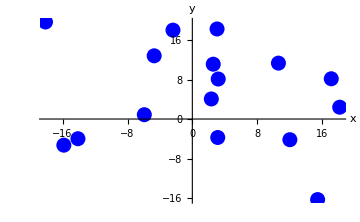

```mathematica
Gdata2=ListPlot[data2, PlotStyle->{Blue, PointSize[0.03]}]
```

```mathematica
(* Set up the basis functions as follows *)
```

```mathematica
Clear[x,t]
```

```mathematica
bf2={x,x^2};
```

```mathematica
p2=LinearModelFit[data2,bf2,x];
```

```mathematica
p2[t]
```

7.83494-0.164611 t-0.019846 t^2

```mathematica
bf3={x,x^2,x^3}
```

{x,x^2,x^3}

```mathematica
p3=LinearModelFit[data2,bf3,x];
```

```mathematica
p3[x]
```

7.56371+0.0984032 x-0.0186898 x^2-0.00105215 x^3

```mathematica
(* Plot the polynomials and the data   *)
```

```mathematica
PR=Max[Abs[xmin2],Abs[xmax2]];
```

```mathematica
GPol2=Plot[{p2[t1],p3[t1]},{t1,-PR,PR},PlotRange->PR];
```

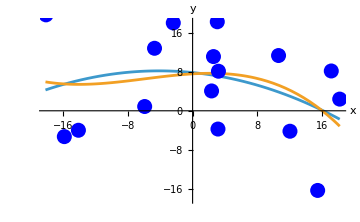

```mathematica
Show[GPol2,Gdata2]
```

```mathematica
(* Show the error - Residuals   *)
```

```mathematica
Abs[p2["FitResiduals"]]
```

{10.7483,3.27573,10.193,7.23676,4.11576,10.8646,0.997502,8.97474,7.16602,11.0885,7.47387,3.8264,15.3491,4.63246,9.88592,16.8599}

```mathematica
Res[p_]:=Abs[p["FitResiduals"]]
```

```mathematica
Lendata2=Dimensions[data2][[1]]
```

16

```mathematica
Ep2=Res[p2]
```

{10.7483,3.27573,10.193,7.23676,4.11576,10.8646,0.997502,8.97474,7.16602,11.0885,7.47387,3.8264,15.3491,4.63246,9.88592,16.8599}

```mathematica
Ep3=Res[p3]
```

{10.7926,3.61357,9.39878,5.6666,5.55067,11.3973,0.450894,9.69904,8.39309,10.5763,6.08211,3.42934,13.7461,6.0063,10.7643,17.0431}

```mathematica
(* The least square Error *)
```

```mathematica
LSE[E_]:=Sqrt[Sum[E[[i]]^2,{i,Lendata2}]]
```

```mathematica
{LSE[Ep2],LSE[Ep2],LSE[Ep3]}
```

{37.1873,37.1873,36.9783}

```mathematica
(* Use different basis functions. Trigonometric system {sin[2Pi i x/N], cos[2Pi i x/N]} *)
```

```mathematica
(* Generate basis functions. The basis includes 4 functions *)
```

```mathematica
Triglist=Table[{Sin[2*Pi*x*i/20],Cos[2*Pi*x*i/20]},{i,1,2}]
```

{{Sin[(π x)/10],Cos[(π x)/10]},{Sin[(π x)/5],Cos[(π x)/5]}}

```mathematica
(* Delete internal brackets *)
```

```mathematica
Triglist=Flatten[Triglist,1]
```

{Sin[(π x)/10],Cos[(π x)/10],Sin[(π x)/5],Cos[(π x)/5]}

```mathematica
(* Fit *)
```

```mathematica
TrigF=LinearModelFit[data2,Triglist,x];
```

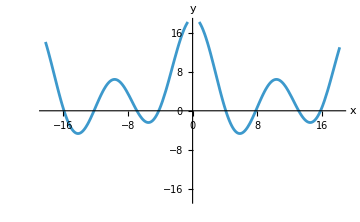

```mathematica
GTrigPol=Plot[TrigF[x],{x,-PR,PR},PlotRange->PR]
```

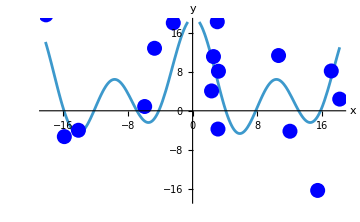

```mathematica
Show[GTrigPol,Gdata2]
```

```mathematica
(* Point Error  *)
```

```mathematica
ETrig=Res[TrigF]
```

{5.1022,6.90139,0.667321,2.98896,10.6142,9.52717,2.6978,1.39168,7.62776,11.892,4.97662,1.65988,5.91692,14.3633,8.38609,15.1678}

```mathematica
(* Least square error  *)
```

```mathematica
LSE[ETrig]
```

32.6269

```mathematica
(* Problem 4 *)
```

```mathematica
Clear[x]
```

```mathematica
data3= data2;
```

```mathematica
bf5={x,x^2,x^3,x^5};
```

```mathematica
bf6sac={x,Sin[x],Cos[x],x^2,ArcTan[x]};
```

```mathematica
bf7trig=Table[{Sin[n*x],Cos[n*x]},{n,1,5}]
```

{{Sin[x],Cos[x]},{Sin[2 x],Cos[2 x]},{Sin[3 x],Cos[3 x]},{Sin[4 x],Cos[4 x]},{Sin[5 x],Cos[5 x]}}

```mathematica
problem401=LinearModelFit[data3,bf5,x]
```

FittedModel[…]

```mathematica
problem402=LinearModelFit[data3,bf6sac,x]
```

FittedModel[…]

```mathematica
b7=Flatten[bf7trig,1]
```

{Sin[x],Cos[x],Sin[2 x],Cos[2 x],Sin[3 x],Cos[3 x],Sin[4 x],Cos[4 x],Sin[5 x],Cos[5 x]}

```mathematica
problem403=LinearModelFit[data3,b7,x]
```

FittedModel[…]

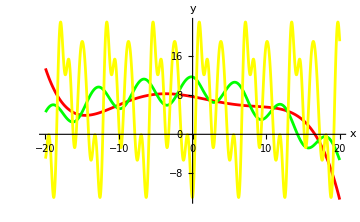

```mathematica
P4PlotAll = Plot[{problem401[x],problem402[x],problem403[x]},{x,-20,20}, PlotStyle->{Red,Green,Yellow}]
```

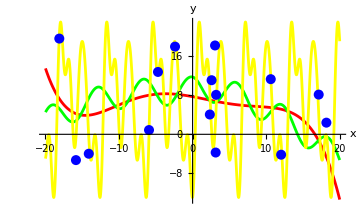

```mathematica
P4PlotAllPlusPoint = Show[{P4PlotAll, ListPlot[data3, PlotStyle->{Blue, PointSize[0.02]}]}]
```

```mathematica
Ep5=Res[problem401]
```

{9.53208,2.94782,7.91557,7.1484,7.06082,10.5122,1.3502,9.46342,9.33478,11.4401,5.82392,4.16544,12.3517,4.53969,9.75948,18.564}

```mathematica
Ep6=Res[problem402]
```

{8.07223,2.87263,11.4126,9.83513,2.8869,10.3555,1.44976,9.39174,10.3199,11.6653,6.6923,4.43368,14.3806,5.08462,10.5063,13.6232}

```mathematica
Ep7=Res[problem403]
```

{4.5777,4.73229,3.37338,0.673634,2.55893,7.08688,2.79882,3.88014,2.38923,17.4687,0.454445,10.2747,0.62307,0.562032,0.989685,13.9903}

```mathematica
(* The LSE *)
```

```mathematica
{LSE[Ep5],LSE[Ep6],LSE[Ep7]}
```

{36.7066,36.6323,27.366}